# Dynamic

Description
We study the time evolution of the system for a particular initial state corresponding to one of the basis vectors.
We plot the magnetization of each site, with a magnetization of 0.5 corresponding to an upspin, and a magnetization
of -0.5 corresponding to a downspin.
We also plot the probability of finding each of the basis vectors is time.
(The code provided here is used to obtain Figure 2 in the paper).

Parameters explained
*) initialstate =initial state corresponding to one of the site-basis vectors
*) endtime = how many times the loop for time is repeated (choice depends on the system)
*) increment = dt = discrete interval of time (choice depends on the system)
*) Psi[t] = evolved state
*) Magsite = magnetization of each site

Code for the Dynamics

Hamiltonian, eigenvalues and eigenstates

.9f

Magnetization of each site

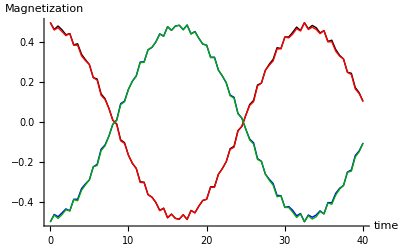

Probability of each site-basis

```mathematica
(*Parameters of the Hamiltonian*)
Clear[chainsize,upspins,downspins,dim,Jxy,Jz,open];
chainsize=4;
upspins=2;
downspins=chainsize-upspins;
dim=chainsize!/(upspins!downspins!);
Jxy=1.0;
Jz=10;
open=1;
(*Creating the basis*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(*ELEMENTS OF THE HAMILTONIAN*)
(*Initialization*)
Clear[HH];
Do[Do[HH[i,j]=0.,{j,1,dim}],{i,1,dim}];

(*Diagonal elements-Ising interaction*)
Do[
Do[
HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,k]]+basis[[i,k+1]]);
       ,{k,1,chainsize-1}];
,{i,1,dim}];
(*Term included in the Ising interaction if the chain is closed*)
If[open==0,
Do[HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,chainsize]]+basis[[i,1]]),
{i,1,dim}]];

(*Off-diagonal elements-flip-flop term*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0
Do[site[z]=0,{z,1,chainsize}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]≠basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];,{k,1,chainsize}];
(*Coupling matrix element-when only two neighbor sites differ*)
If[howmany==2,If[site[2]-site[1]==1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
(*Additional term for closed system*)If[open==0, If[site[2]-site[1]==chainsize-1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
,{j,i+1,dim}];
,{i,1,dim-1}];

(* TOTAL HAMILTONIAN AND DIAGONALIZATION *)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];

(*Choose an initial state*)
Do[
If[basis[[i,1]]==1 && basis[[i,3]]==1,initialstate=i];
,{i,1,dim}];

(*DYNAMICS*)
Clear[endtime,PSI,increment,Magsite];
endtime=81;
increment=0.5;
Do[PSI[t]=Sum[Vector[[j,initialstate]]Vector[[j]] Exp[-I Energy[[j]](t-1) increment],{j,1,dim}];
(*Magnetization*)
Do[Magsite[j,t]=0.5 Sum[Abs[PSI[t][[i]]]^2(-1.)^(1+basis[[i,j]]),{i,dim}];
,{j,1,chainsize}];
(*Print[{(t-1)increment,Magsite[1,t]}];*)
,{t,1,endtime}];
.9f 
(*Call Package for Legends*)
<<PlotLegends`
Clear[magT,ProbT];
Do[magT[j]=Table[{(t-1) increment,Magsite[j,t]},{t,1,endtime}],{j,1,chainsize}];
Do[ProbT[k]=Table[{(t-1) increment,Abs[PSI[t][[k]]]^2},{t,1,endtime}],{k,1,dim}];

Print[];
Print["Magnetization of each site"];
ListPlot[Table[magT[j],{j,1,chainsize}],PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Red},{Thick,Darker[Green]} },LabelStyle->Directive[Black,Bold,Medium],PlotLegend->Table["site"[x],{x,1,dim}],LegendPosition->{1,0},AxesLabel->{"time","Magnetization"}]

Print[];
Print["Probability of each site-basis"];
ListPlot[Table[ProbT[k],{k,1,dim}],PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Red},{Thick,Darker[Green]},{Thick,Magenta},{Thick,Brown} },LabelStyle->Directive[Black,Bold,Medium],PlotLegend->Table[basis[[k]],{k,1,dim}],LegendPosition->{1,0},LegendSize->{1,1},AxesLabel->{"time","Probability"},Frame->True,FrameLabel->{{"Probability",""},{"Jt","Δ=10"}}]
```